# Laborotoria 5

## Wprowadzenie do równań różniczkowych zwyczajnych

Jak sprawdzić czy funkcja jest rozwiązaniem równania różniczkowego

```mathematica
y[x_] := c Exp[-x^2]
y'[x] + 2 x y[x] == 0
```

True

```mathematica
Clear[y]
```

```mathematica
y'[x] == 2 x y[x]^2 - x^2 y'[x]/. y[x] -> 1/(const - Log[x^2 +1])
```

y'[x]==(2 x)/((const-Log[1+x^2])^2)-x^2 y'[x]

```mathematica
y'[x] == 2 x y[x]^2 - x^2 y'[x]/. y->Function[x,1/(const - Log[x^2 +1])]
```

(2 x)/((1+x^2) (const-Log[1+x^2])^2)==(2 x)/((const-Log[1+x^2])^2)-(2 x^3)/((1+x^2) (const-Log[1+x^2])^2)

```mathematica
Simplify[%]
```

simplify[True]

Jak znaleźć równanie różniczkowe (możliwie niskiego rzędu), które opisuje rodzinę krzywych?

```mathematica
eq = y[x] == c Exp[-x^2]
```

y[x]==c ⅇ^(-x^2)

```mathematica
D[eq, x]
```

y'[x]==-2 c ⅇ^(-x^2) x

```mathematica
Solve[eq, c]
```

{{c→ⅇ^(x^2) y[x]}}

```mathematica
D[eq, x]/. First@Solve[eq, c]
```

y'[x]==-2 x y[x]

## Rozwiązania analityczne

Mathematica ma uniwersalą funkcję do rozwiązywania równań różniczkowych:

```mathematica
sol=DSolve[y'[x] == -y[x] Cos[x],y[x],x]
```

{{y[x]→ⅇ^(-Sin[x]) C[1]}}

```mathematica
solutions = Table[y[x]/. First@sol/. C[1] -> {i, -5, 5}]
```

{ⅇ^(-Sin[x]) i,-5 ⅇ^(-Sin[x]),5 ⅇ^(-Sin[x])}

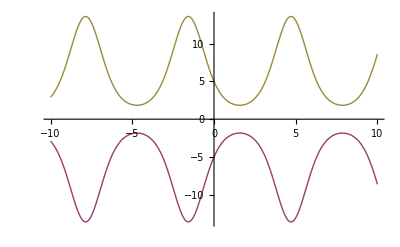

```mathematica
Plot[solutions, {x, -10, 10}]
```

```mathematica
sol = DSolve[y''[x] +y[x] == 0, y, x]
```

{{y→Function[{x},C[1] Cos[x]+C[2] Sin[x]]}}

```mathematica
solutions1 = Table[y[x]/.First@sol/. {C[1] -> i, C[2] ->0}, {i,0,5}];
```

```mathematica
solutions2 = Table[y[x]/.First@sol/. {C[1] -> 0, C[2] ->i}, {i,0,5}];
```

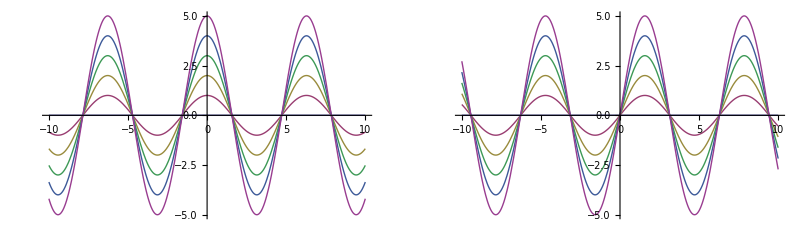

```mathematica
GraphicsRow[{
Plot[solutions1, {x, -10, 10}],
Plot[solutions2, {x, -10, 10}]
}]
```

Jak uwzględnić warunki początkowe?

```mathematica
sol = DSolve[{v'[t]== 32-v[t], v[0] == v0},v[t],t]
```

{{v[t]→ⅇ^-t (-32+32 ⅇ^t+v0)}}

Może się zdarzyć, że Mathematica nie poradzi sobie z równaniem

```mathematica
DSolve[{x''[t]+(1/3(x'[t])^2 -1) x'[t] + x[t] == 0, x[0] == 1, x'[0] == 0}, x[t], t]
```

DSolve[{x[t]+x'[t] (-1+1/3 x'[t]^2)+x''[t]==0,x[0]==1,x'[0]==0},x[t],t]

Możemy rozwiązać równanie numerycznie

```mathematica
sol = NDSolve[{x''[t]+(1/3(x'[t])^2 -1) x'[t] + x[t] == 0, x[0] == 1, x'[0] == 0}, x[t], {t,0,25}]
```

{{x[t]→InterpolatingFunction[{{0.,25.}},<>][t]}}

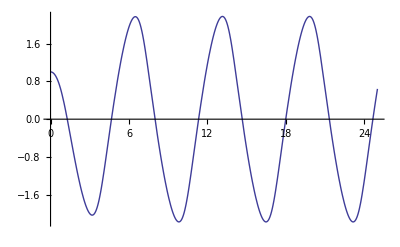

```mathematica
Plot[x[t]/. First@sol, {t,0,25}]
```

## Zadanie 1

```mathematica
eq = x[y]^3 y - c y^2 == c
```

-c y^2+y x[y]^3==c

```mathematica
D[eq, y]
```

-2 c y+x[y]^3+3 y x[y]^2 x'[y]==0

```mathematica
Solve[eq,c]
```

{{c→(y x[y]^3)/(1+y^2)}}

```mathematica
eq1 = D[eq, y]/. Solve[eq, c]
```

{x[y]^3-(2 y^2 x[y]^3)/(1+y^2)+3 y x[y]^2 x'[y]==0}

```mathematica
eq2 = Solve[eq1,x'[y]]
```

{{x'[y]→((-1+y^2) x[y])/(3 y (1+y^2))}}

```mathematica
eq3 = DSolve[x'[y]== ((-1+y^2) x[y])/(3 y (1+y^2)), x[y], y]
```

{{x[y]→ⅇ^(1/3 (-Log[y]+Log[1+y^2])) C[1]}}

```mathematica
solutions= Table[x[y]/.First@eq3/. C[1] -> i, {i,-5,5}]
```

{-5 ⅇ^(1/3 (-Log[y]+Log[1+y^2])),-4 ⅇ^(1/3 (-Log[y]+Log[1+y^2])),-3 ⅇ^(1/3 (-Log[y]+Log[1+y^2])),-2 ⅇ^(1/3 (-Log[y]+Log[1+y^2])),-ⅇ^(1/3 (-Log[y]+Log[1+y^2])),0,ⅇ^(1/3 (-Log[y]+Log[1+y^2])),2 ⅇ^(1/3 (-Log[y]+Log[1+y^2])),3 ⅇ^(1/3 (-Log[y]+Log[1+y^2])),4 ⅇ^(1/3 (-Log[y]+Log[1+y^2])),5 ⅇ^(1/3 (-Log[y]+Log[1+y^2]))}

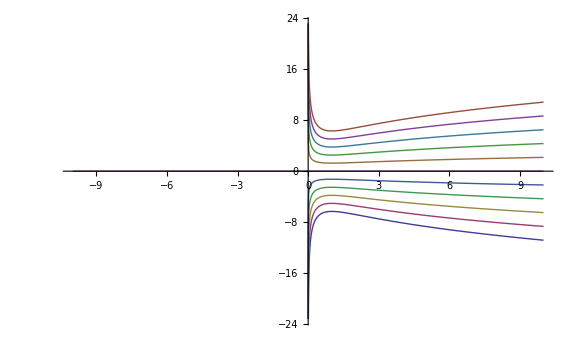

```mathematica
GraphicsRow[
{
Plot[solutions, {y,-10,10}, ImageSize->Large]
}]
```

Rozwiązanie osobliwe to x=0, w pozostałych punktachmamy jednoznaczność rozwiązań.

## Pola kierunków równań zwyczajnych

Dla równań y’ =f(x,y) możemy stworzyć pola kierunków, czyli pole wektorów stycznych do krzywych całkowych:
(1, f(x,y)).

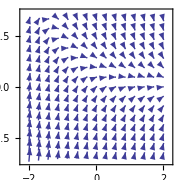

```mathematica
f[x_, y_] := Exp[-x] -2 y
vectpl = VectorPlot[{1, f[x,y]}, {x,-2,2}, {y, -2,2}, ImageSize->Small]
```

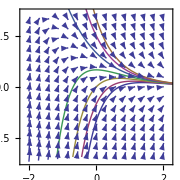

```mathematica
sol = DSolve[y'[x] == f[x, y[x]], y[x], x];
solutions = Table[y[x]/. First@sol/. C[1] -> i, {i, -2,1,0.5}];
Show[
vectpl,
Plot[solutions, {x, -2, 4}]
]
```

Może się zdarzyć, że wykres pola wektorowego będzie nieczytelny:

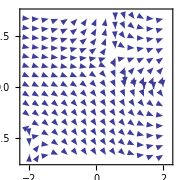

```mathematica
f[x_,y_] := (Cos[y] - y Cos[x])/(x Sin[y] + Sin[x] -1)
VectorPlot[{1, f[x,y]}, {x, -2, 2}, {y, -2, 2}, ImageSize->Small]
```

```mathematica
strpl = StreamPlot[{1, f[x,y]}, {x,-10,10}, {y, -10, 10}]
```

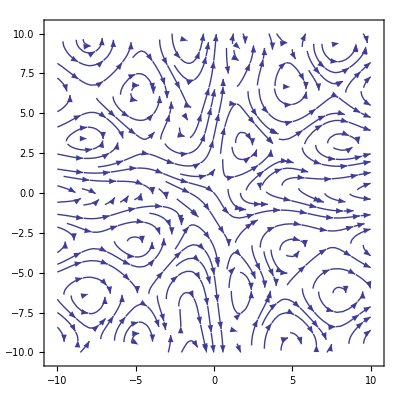

```mathematica
sol = DSolve[y'[x] == f[x, y[x]], y[x], x]
```

Solve[-x Cos[y[x]]-y[x]+Sin[x] y[x]==C[1],y[x]]

```mathematica
solution = (First@First@sol/. y[x] -> y)
```

-y-x Cos[y]+y Sin[x]

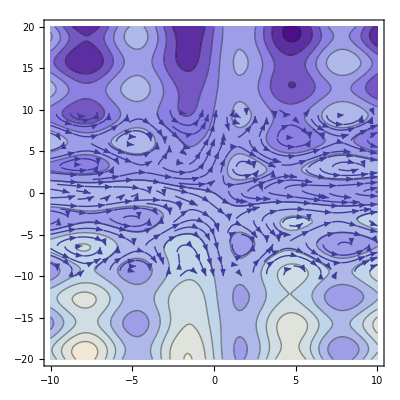

```mathematica
Show[
ContourPlot[ solution, {x, -10, 10}, {y, -20,20}],
strpl
]
```

Wróćmy do równania 2 rzędu:
{x''[t]+(1/3(x'[t])^2 -1) x'[t] + x[t] == 0, x[0] == 1, x'[0] == 0}
Sprowadzimy równanie do układu równań 1 rzędu (autonomicznych): y=x’.
x’ = y= f1(x,y), y’ = x’’ = f2(x,y)

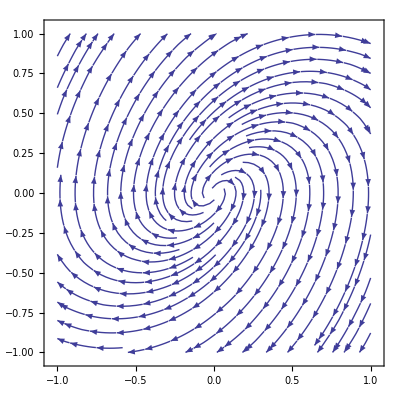

```mathematica
f1[x_,y_] := y
f2[x_, y_] := -(1/3 y^2 -1) y -x
strpl = StreamPlot[{f1[x,y], f2[x,y]}, {x, -1,1}, {y, -1,1}]
```

```mathematica
sol = NDSolve[{x'[t] == f1[x[t], y[t]], y'[t] == f2[x[t], y[t]], x[0] == 1, y[0] == 0},
{x[t], y[t]}, {t,0, 15}]
```

{{x[t]→InterpolatingFunction[{{0.,15.}},<>][t],y[t]→InterpolatingFunction[{{0.,15.}},<>][t]}}

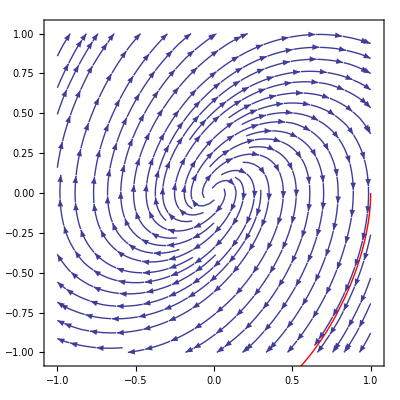

```mathematica
Show[
strpl,
ParametricPlot[{x[t], y[t]}/. First@sol, {t,0,15}, PlotStyle->Red]
]
```

## Zadanie 2

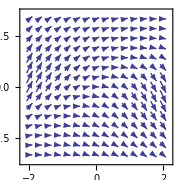

```mathematica
f[t_,x_] := (x-t)/(x^2+1)
vectpl = VectorPlot[{1, f[t,x]}, {t,-2,2}, {x ,-2,2}, ImageSize->Small]
```

```mathematica
pocz1 =NDSolve[{x'[t] ==(x[t]-t)/(x[t]^2+1), x[0]==1},x[t],{t,-10,10}]
```

{{x[t]→InterpolatingFunction[{{-10.,10.}},<>][t]}}

```mathematica
pocz2 = NDSolve[{x'[t] ==(x[t]-t)/(x[t]^2+1), x[0]==0},x[t], {t,-3,3}]
```

{{x[t]→InterpolatingFunction[{{-3.,3.}},<>][t]}}

```mathematica
pocz3 = NDSolve[{x'[t] ==(x[t]-t)/(x[t]^2+1), x[0]==-1},x[t], {t,-3,3}]
```

{{x[t]→InterpolatingFunction[{{-3.,3.}},<>][t]}}

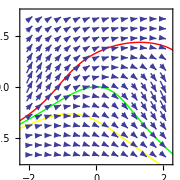

```mathematica
Show[{
vectpl,
Plot[x[t]/.First@pocz1, {t, -3,3}, PlotStyle->Red],
Plot[x[t]/.First@pocz2, {t, -3,3}, PlotStyle->Green],
Plot[x[t]/.First@pocz3, {t, -3,3}, PlotStyle->Yellow]
}]
```

## Zadanie 3

```mathematica
sol = DSolve[x''[t]-6 x'[t] + 9 x[t] == 9 t^2 -12 t +2, x[t], t]
```

{{x[t]→t^2+ⅇ^(3 t) C[1]+ⅇ^(3 t) t C[2]}}

```mathematica
solutions1 = Table[x[t]/.First@sol/. {C[1] -> i, C[2] ->0}, {i,0,5}];
solutions2 = Table[x[t]/.First@sol/. {C[1] -> 0, C[2] ->i}, {i,0,5}]
```

{t^2,ⅇ^(3 t) t+t^2,2 ⅇ^(3 t) t+t^2,3 ⅇ^(3 t) t+t^2,4 ⅇ^(3 t) t+t^2,5 ⅇ^(3 t) t+t^2}

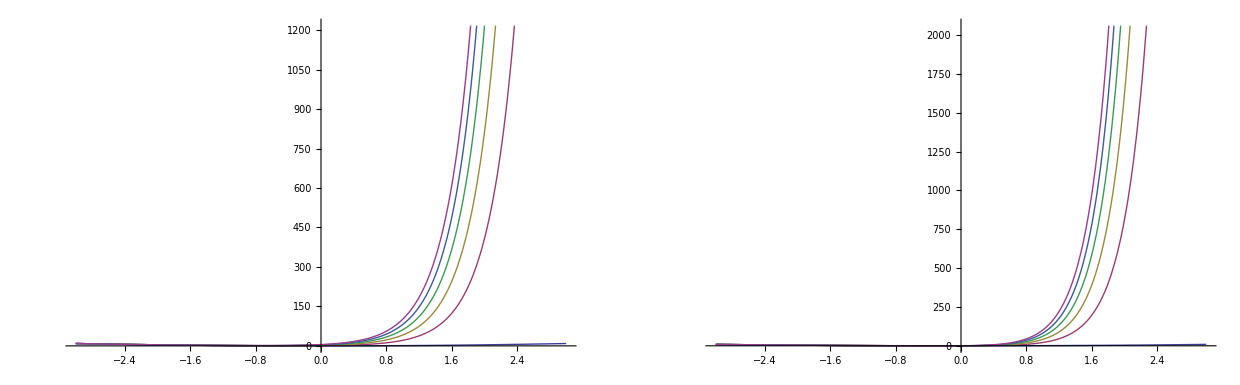

```mathematica
GraphicsRow[{
Plot[solutions1, {t, -3, 3}, ImageSize->Large],
Plot[solutions2, {t, -3, 3}, ImageSize->Large]
}]
```